Контролна № -1 на Никола Тотев, ФН - 62271, Група - 6

```mathematica
(*Exercise 1*)
```

```mathematica
(*TO DO - COMPLETE EXERCISE 1*)
```

```mathematica
(*Exercise 2*)
```

```mathematica
x0 = -1;
x1  = -0.5;
x2=0;
x3=0.5;
x4 = 1;
givenFunction[x_] = 1/(25+x^2);
```

```mathematica
fifthDerivative[x_]= D[givenFunction[x], {x, 5}];
```

```mathematica
W[x_] = (x-x0)(x-x1)(x-x2)(x-x3)(x-x4);
R[x_] = (fifthDerivative[x]/(5!))*W[x];
R[x]
```

1/120 (-1+x) (-0.5+x) x (0.5+x) (1+x) (-(3840 x^5)/((25+x^2)^6)+(3840 x^3)/((25+x^2)^5)-(720 x)/((25+x^2)^4))

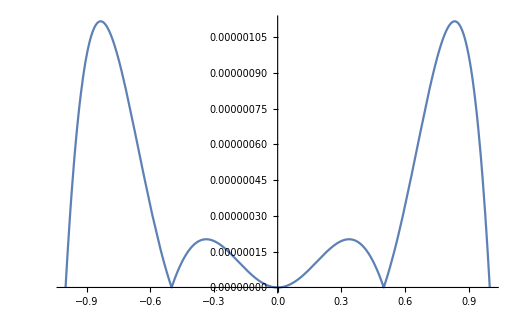

```mathematica
errEstimationPlot = Plot[Abs[R[x]], {x, -1, 1}];
errEstimationPlot
```

```mathematica
(*Exercise 3*)
```

```mathematica
LagrangeBasic[k_, nodes2_,x_] := (
basicPoly = 1;
For[i=1, i≤ Length[nodes2], i++,If[i==k,basicPoly*=1, basicPoly*=(x-nodes2[[i]])/(nodes2[[k]]- nodes2[[i]])]];
basicPoly;
);
```

```mathematica
Lagrange[nodes_, functionToInterpolate_, x_]:= (
values = functionToInterpolate[nodes];(*Using Table[]?*)
finalPoly=0 ;
For[j=1, j≤ Length[nodes], j++, finalPoly+=( values[[j]]*LagrangeBasic[j, nodes, x])];
finalPoly;
);
```

```mathematica
testNodes={-1,0.5,0,-0.5, 1};
testPoly[x_] = Lagrange[testNodes,1+x,x];
values
```